```mathematica
Clear["Global`*"];
nodelist={{0,0},{2,0},{0,2}};
tri=Polygon[nodelist];
tri
```

Polygon[…]

```mathematica
res=NDSolveValue[{-∇_{x,y}^2 u[x,y] == 
   NeumannValue[1., x ==0], 
  DirichletCondition[u[x, y] == 0., y ==0]}, u, {x, y} ∈ 
  tri]
```

InterpolatingFunction[…]

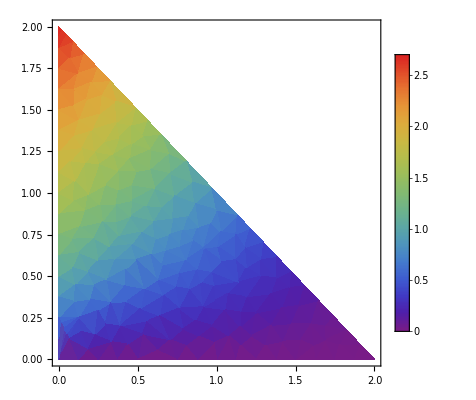

```mathematica
figure=DensityPlot[res[x,y],{x,y}∈tri,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
Export["..//Desktop//problem1_mma_solution.pdf",figure];
Export["..//Desktop//problem1_mma_solution.png",figure]
```

..//Desktop//problem1_mma_solution.png